```mathematica
tab1[n_]  := Table[{x,Sin[x]^2 + E^x},{x,-1,1,2/n}]
tab2[n_] := Join[Table[{x,Sin[x]^2},{x,-1,0,2/n}],Reverse[Table[{x,x^2+x^3},{x,1,1/(10 n),-2/n}]]]
```

```mathematica
func1=Sin[x]^2+E^x
func2=If[x≤0,Sin[x]^2,x^2+x^3]
```

ⅇ^x+Sin[x]^2

If[x≤0,Sin[x]^2,x^2+x^3]

```mathematica
tab1[2]//N
tab2[2]//N
```

{{-1.,1.07595},{0.,1.},{1.,3.42636}}

{{-1.,0.708073},{0.,0.},{1.,2.}}

```mathematica
poli1 = Table[InterpolatingPolynomial[tab1[n],x],{n,2,10}];
errox1=Table[poli1[[i]]-func1,{i,1,Length[poli1]}];
```

```mathematica
poli1[[9]]//N//Expand
```

1.+1. x+1.5 x^2+0.166667 x^3-0.291666 x^4+0.00833335 x^5+0.0458313 x^6+0.000198371 x^7-0.00314309 x^8+2.81136×10^-6 x^9+0.000132262 x^10

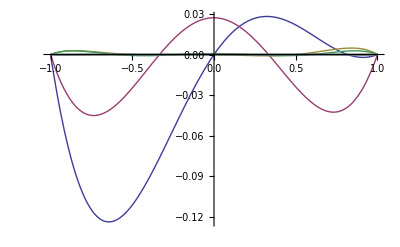

```mathematica
Plot[errox1,{x,-1,1},PlotRange->All]
```

```mathematica
tab2[2]
```

{{-1,Sin[1]^2},{0,0},{1,2}}

```mathematica
InterpolatingPolynomial[tab2[2],x]
```

Sin[1]^2+(1+x) (-Sin[1]^2+1/2 x (2+Sin[1]^2))

```mathematica
poli2=Table[InterpolatingPolynomial[tab2[n],x],{n,2,10}];
errox2=Table[poli2[[i]]-func2,{i,1,Length[poli2]}];
```

```mathematica
tab2[2]//N
tab2[3]//N
tab2[4]//N
tab2[5]//N
```

{{-1.,0.708073},{0.,0.},{1.,2.}}

{{-1.,0.708073},{-0.333333,0.107056},{0.333333,0.148148},{1.,2.}}

{{-1.,0.708073},{-0.5,0.229849},{0.,0.},{0.5,0.375},{1.,2.}}

{{-1.,0.708073},{-0.6,0.318821},{-0.2,0.0394695},{0.2,0.048},{0.6,0.576},{1.,2.}}

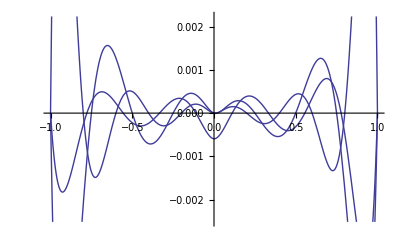

```mathematica
Plot[Take[errox2,-3],{x,-1,1}]
```

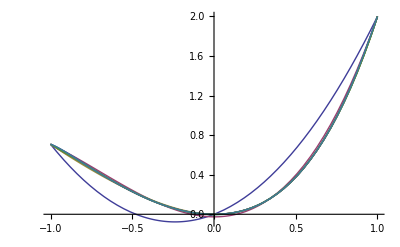

```mathematica
Plot[poli2,{x,-1,1}]
```

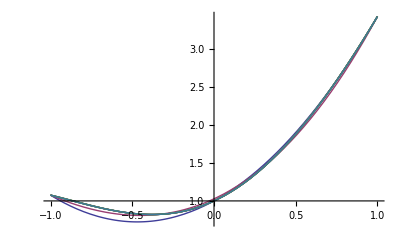

```mathematica
Plot[poli1,{x,-1,1}]
```

{{2,-2.44476},{3,-3.23946},{4,-5.92758},{5,-6.32771},{6,-9.70318},{7,-10.0834},{8,-13.7592},{9,-14.1313},{10,-18.141}}

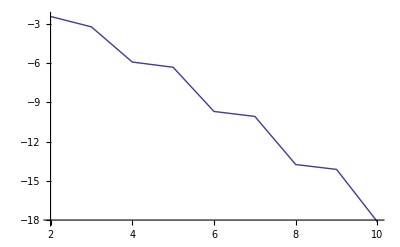

```mathematica
erro1L2=Table[{i+1,Log[Sqrt[NIntegrate[errox1[[i]]^2,{x,-1,1}]]]},{i,1,Length[errox1]}]
ListPlot[erro1L2,PlotJoined->True]
```

{{2,-1.3286},{3,-3.60345},{4,-4.65947},{5,-5.30754},{6,-5.46807},{7,-6.1953},{8,-5.72627},{9,-6.60845},{10,-5.61179}}

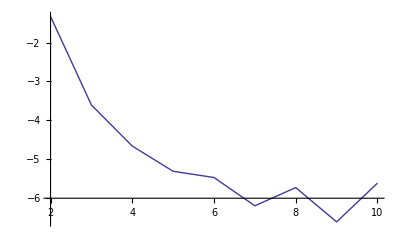

```mathematica
erro2L2=Table[{i+1,Log[Sqrt[NIntegrate[errox2[[i]]^2,{x,-1,1}]]]},{i,1,Length[errox2]}]
ListPlot[erro2L2,PlotJoined->True]
```

{{2,-1.14854},{3,-1.62681},{4,-3.90308},{5,-4.14591},{6,-7.24525},{7,-7.51141},{8,-10.9839},{9,-11.2657},{10,-15.1156}}

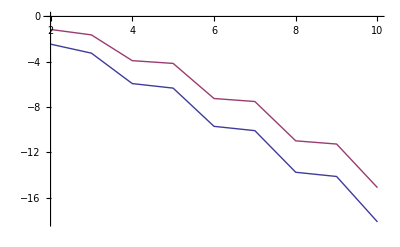

```mathematica
erro1H1=Table[{i+1,Log[Sqrt[NIntegrate[errox1[[i]]^2+D[errox1[[i]],x]^2,{x,-1,1}]]]},{i,1,Length[errox1]}]
ListPlot[{erro1L2,erro1H1},PlotJoined->True]
```

{{2,-0.0982531},{3,-2.00868},{4,-2.73636},{5,-3.18901},{6,-3.09743},{7,-3.6954},{8,-3.02623},{9,-3.80669},{10,-2.65003}}

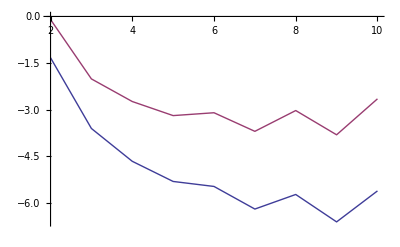

```mathematica
erro2H1=Table[{i+1,Log[Sqrt[NIntegrate[errox2[[i]]^2+D[errox2[[i]],x]^2,{x,-1,1}]]]},{i,1,Length[errox2]}]
ListPlot[{erro2L2,erro2H1},PlotJoined->True]
```

```mathematica
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}]
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}]
```

```mathematica
InterpolatingPolynomial[poli3[1,3],x]
```

1+(-1+x/2) (1+x)

```mathematica
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],x],{i,1,n}]
```

```mathematica
ListPoli[2]
```

{1+1/2 (-1-x),(1+x)/2}

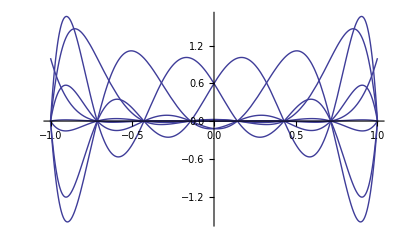

```mathematica
Plot[ListPoli[8],{x,-1,1}]
```

```mathematica
tab3[1,2]
```

{1,0}